```mathematica
"Manuel de la Cruz González  7090970H"
```

```mathematica
"Entrega 3.
```

```mathematica
"Ejercicio 1:
```

```mathematica
Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Entrega 3\\Ej 1\\derivada.txt","Table"]
```

{{0.001,-0.484357,-0.484023,-0.484356,0.00008169,-0.06876,-9.667×10^-7},{0.002,-0.484358,-0.483691,-0.484356,0.0003297,-0.1373,-9.669×10^-7},{0.003,-0.48436,-0.48336,-0.484356,0.0007429,-0.2058,-9.683×10^-7},{0.004,-0.484363,-0.483029,-0.484356,0.001322,-0.274,-9.718×10^-7},{0.005,-0.484366,-0.482699,-0.484356,0.002065,-0.3421,-9.792×10^-7},{0.006,-0.484371,-0.48237,-0.484356,0.002975,-0.4101,-9.927×10^-7},{0.007,-0.484376,-0.482042,-0.484356,0.004049,-0.4778,-1.015×10^-6},{0.008,-0.484382,-0.481714,-0.484356,0.005289,-0.5455,-1.049×10^-6},{0.009,-0.484389,-0.481388,-0.484356,0.006695,-0.6129,-1.099×10^-6},{0.01,-0.484396,-0.481062,-0.484356,0.008265,-0.6802,-1.168×10^-6}}

```mathematica
Esta es la tabla que conseguimos con el programa.
```

```mathematica
Las columnas de izda a derecha son:
```

```mathematica
Valores del paso h, aceleración por la fórmula simétrica, la formula no simétrica, la fórmula de richardson y sus errores relativos respectivamente.
```

```mathematica
"Parte de Mathematica:"
```

```mathematica
"a) Gráfica de la velocidad"
```

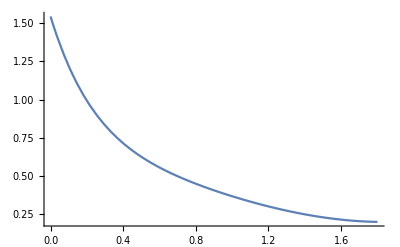

```mathematica
Plot[Exp[-x]Cosh[(1-x)^2],{x,0,1.8}]
```

```mathematica
"EJERCICIO 2:"
```

```mathematica
"Parte de Mathematica:"
```

```mathematica
"Valor numérico de la derivada"
```

```mathematica
NIntegrate[Exp[-x]Cosh[(1-x)^2],{x,0,1.8}]
```

0.930797

```mathematica
"Cálculo de los pesos en Newton Cotes de 5 puntos (n=4):"
```

```mathematica
a=0
b=1.8
h=(b-a)/4;
x0=a;
x1=a+h;
x2=a+2h;
x3=a+3h;
x4=b;

i0=Integrate[1, {x,a,b}];
i1=Integrate[x, {x,a,b}];
i2=Integrate[x^2, {x,a,b}];
i3=Integrate[x^3, {x,a,b}];
i4=Integrate[x^4, {x,a,b}];
s0[a0_,a1_,a2_,a3_,a4_]:=a0+a1+a2+a3+a4;
s1[a0_,a1_,a2_,a3_,a4_]:=a0 x0+a1 x1+a2 x2+a3 x3+a4 x4;
s2[a0_,a1_,a2_,a3_,a4_]:=a0(x0 x0)+a1(x1 x1)+a2 (x2 x2)+a3 (x3 x3)+a4 (x4 x4);
s3[a0_,a1_,a2_,a3_,a4_]:=a0(x0 x0 x0)+a1(x1 x1 x1)+a2 (x2 x2 x2)+a3 (x3 x3 x3)+a4 (x4 x4 x4);
s4[a0_,a1_,a2_,a3_,a4_]:=a0(x0 x0 x0 x0)+a1(x1 x1 x1 x1)+a2 (x2 x2 x2 x2)+a3 (x3 x3 x3 x3)+a4 (x4 x4 x4 x4);
Solve[{i0== s0[a0,a1,a2,a3,a4],i1== s1[a0,a1,a2,a3,a4], i2== s2[a0,a1,a2,a3,a4],i3==s3[a0,a1,a2,a3,a4], i4==s4[a0,a1,a2,a3,a4]},{a0,a1,a2, a3,a4}]
```

0

1.8

{{a0→0.14,a1→0.64,a2→0.24,a3→0.64,a4→0.14}}

```mathematica
"El valor de la integral en el intervalo [0,1.8] calculado con diferentes métodos con sus errores relativos son:
```

```mathematica
"Punto medio:
```

```mathematica
Valor: 0.731861979107      Error:0.2137
```

```mathematica
"Trapecio simple:
```

```mathematica
Valor:1.56906373589     Error: 0.6852
```

```mathematica
"Regla de Simpson simple:
```

```mathematica
Valor:1.01092923137    Error:8.6089x 10^-2
```

```mathematica
"Newton-Cotes: En Newton Cotes hay un error
```

```mathematica
"Gauss-Legendre 2 puntos:
```

```mathematica
Valor: 0.88214891    Error:5.2265 x10^-2
```

```mathematica
"Gauss-Legendre 10 puntos:
```

```mathematica
Valor: 0.930797305279    Error:2.84 x10^-8
```

```mathematica
"Simpson compuesta:
```

```mathematica
Valor:0.9049398390     Error: 2.778 x10^-2
```

```mathematica
"Podemos observar que el método más preciso es el de Gauss-Legendre con 10 puntos, aunque también es en el que más información hemos utilizado. El más impreciso ha sido el del trapecio simple pues es una aproximación poco precisa.
```

```mathematica
EJERCICIO 3
```

```mathematica
"La integral del recinto delimitado por las curvas calculada mediante nuestro programa de Fortran ha sido:
```

```mathematica
Valor Fortran: 2.63502218796
```

```mathematica
Error relativo: 9.323898 x10^-9
```

```mathematica
"Al haber aplicado también el método de Gauss-Legendre de 10 puntos como en el ejercicio anterior, hemos obtenido un error del mismo orden de magnitud.
```

```mathematica
"Parte de Mathematica: "
```

```mathematica
"Valor numérico de la integral"
```

```mathematica
g[x_,y_]:=((x)^2+(y)^2)*Exp[-(x*y)]
```

```mathematica
l1[x_]:=0
```

```mathematica
l2[x_]:=1+x
```

```mathematica
NIntegrate[g[x,y],{x,2,3},{y,l1[x],l2[x]}]
```

2.63502

```mathematica
"Como vemos coincide con el valor obtenido en Fortran."
```